```mathematica
$Assumptions=μ>0&&σ>0&&a ∈ Reals&&1≥k1≥0&&k0≥0&&S0>0&&K>0&&r≥0&&b ∈ Reals&& rf≥0
```

μ>0&&σ>0&&a∈Reals&&1≥k1≥0&&k0≥0&&S0>0&&K>0&&r≥0&&b∈Reals&&rf≥0

```mathematica
u[x_]:=Abs[x]^2
u1=Abs @*InverseFunction[u]
p[n_,f_]:=Module[{e=n[f[x],x\[Distributed]NormalDistribution[]]},
Simplify[Exp[-r]e+rf u1[n[u[Exp[-r](f[x]-e)],x\[Distributed]NormalDistribution[]]]]]
S[a_]:=a Exp[μ -σ^2/2+σ #]&
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Abs@*(-√#1&)

```mathematica
p[Expectation,S[a]]
```

ⅇ^(-r+μ) (a+√(-1+ⅇ^(σ^2)) rf Abs[a])

```mathematica
(* a = Sig[phi] *)
```

```mathematica
g[a_,k1_]:=Simplify[ p[Expectation,S[(a+k1)]]-a]
```

```mathematica
g[a,k1]
```

-a+ⅇ^(-r+μ) (a+k1+√(-1+ⅇ^(σ^2)) rf Abs[a+k1])

```mathematica
g[1,k1]
```

-1+ⅇ^(-r+μ) (1+k1) (1+√(-1+ⅇ^(σ^2)) rf)

```mathematica
Expand[Simplify[rf(1+k1)Solve[-1+ⅇ^(-r+μ) (1+rf s) (1+k1)+x==0,s][[1,1,2]]]]
```

-1+ⅇ^(r-μ)-k1-ⅇ^(r-μ) x

```mathematica
(* arbitrage happens if equation ≠ 0 for x=k1. solve this for √(-1+ⅇ^(σ^2))*)
```

```mathematica
l1=(-1+Exp[r-μ](1-k1)/(1+k1))/rf;Simplify[-1+ⅇ^(-r+μ) (1+rf l1) (1+k1)+k1]
```

0

```mathematica
g[-1,k1]
```

1-ⅇ^(-r+μ) (-1+k1) (-1+√(-1+ⅇ^(σ^2)) rf)

```mathematica
Expand[Simplify[rf (1-k1)Solve[1-ⅇ^(-r+μ) (-1+rf s) (-1+k1)+x==0,s][[1,1,2]]]]
```

1-ⅇ^(r-μ)-k1-ⅇ^(r-μ) x

```mathematica
(* arbitrage happens if equation ≠ 0 for x=k1. solve this for √(-1+ⅇ^(σ^2))*)
```

```mathematica
l2=(1-Exp[r-μ](1+k1)/(1-k1))/rf;Simplify[1-ⅇ^(-r+μ) (-1+rf l2) (-1+k1)+k1]
```

0

```mathematica
g1[a_,b_,k1_]:=Simplify[ p[Expectation,S[(b+a+k1)]]-a]
```

```mathematica
g1[a,b,k1]
```

-a+ⅇ^(-r+μ) (a+b+k1+√(-1+ⅇ^(σ^2)) rf Abs[a+b+k1])

```mathematica
g2[a_,k1_]:=Simplify[p[Max[0,K- S[#]]+
 S[#]&]-a ]
```

```mathematica
g2[a,k1]
```

-a+p[Max[0,K-S[#1]]+S[#1]&]

```mathematica
Plot[W[10/x],{k,0,10}]
```

-Graphics-

```mathematica
μ=0.1;σ=0.1;
```

```mathematica
μ=.;σ=.;
```

```mathematica
Expand[Normal[Series[U[x-e],{e,0,4}]]]
```

U[x]-e U'[x]+1/2 e^2 U''[x]-1/6 e^3 U^(3)[x]+1/24 e^4 U^(4)[x]

```mathematica
Plot3D[(1+a b)/(1+a),{a,-5,5},{b,0,2}]
```

-Graphics3D-

```mathematica
a=0.5
```

0.5

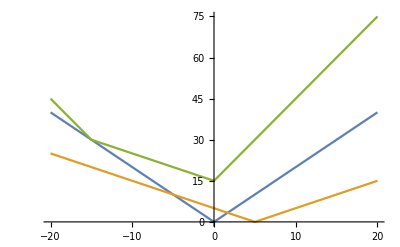

```mathematica
a=2.;b=5;Plot[{a Abs[x], Abs[b-x],a Abs[x]+ Abs[15+x]},{x,-20,20}]
```

```mathematica
Series[(1+x)/(1-x),{x,0,5}]
```

1+2 x+2 x^2+2 x^3+2 x^4+2 x^5+O[x]^6

```mathematica
Sqrt[Log[2]]//N
```

0.832555

## Multiple Periods

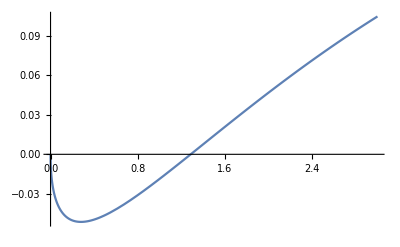

```mathematica
s=0.2;r=-0.2;Plot[{-s √t+1-Exp[r t]},{t,0,3}]
```